# imaging moveout approximation

## imaging moveout

```mathematica
Clear["Global`*"]
```

```mathematica
z0=Simplify[(1-√(1+2 delta) √(1+2 eta) p v0)/(√(1+2 delta) √(1+2 eta) G p)]
```

(1/(√(1+2 delta) √(1+2 eta) p)-v0)/G

```mathematica
x0=Simplify[(√(1-(1+2 delta) (1+2 eta) p^2 v0^2))/(G p √(1-2 (1+2 delta) eta p^2 v0^2))];
```

## for t0

```mathematica
vn0=Sqrt[1+2*delta]*v0;
```

```mathematica
R1=1-(1+2*eta)*p^2*vn0^2;
```

```mathematica
R2=1-2*eta*p^2*vn0^2;
```

```mathematica
p1=Simplify[Sqrt[R1/R2]];
```

```mathematica
p2=Simplify[Log[(Sqrt[R1]+Sqrt[R2])/(Sqrt[1+2 delta]*p*v0)]];
```

```mathematica
p3=Simplify[1/2*Sqrt[(1+2*eta)/(2*eta)]*Log[1+4*eta*R1-2*Sqrt[2*eta*(1+2*eta)*R1*R2]]];
```

```mathematica
t0=Simplify[(p1+p2+p3)/G];
```

## imaging moveout (epslion & eta)

#### sensitivity with epslion

```mathematica
Zpp=(v0 (-p^2 v0^2-ⅇ^(4 G t0) p^2 v0^2+2 ⅇ^(2 G t0) (-2+p^2 v0^2)-2 ⅇ^(G t0) (-1+√(1-p^2 v0^2))+2 ⅇ^(3 G t0) (1+√(1-p^2 v0^2))))/(G (p^2 v0^2+ⅇ^(4 G t0) p^2 v0^2+ⅇ^(2 G t0) (4-2 p^2 v0^2)))/.delta->((1+2*epslion)/(1+2*eta)-1)/2;
```

```mathematica
Xp=(Sqrt[1-p^2*v0^2]-Sqrt[1-p^2*(v0+G*Zpp)^2])/(p*G);
```

```mathematica
Dxp=x0-Xp/.delta->((1+2*epslion)/(1+2*eta)-1)/2;
```

```mathematica
parame={v0->2,G->0.5,epslion->0.3,eta->0.15}
```

{v0→2,G→0.5,epslion→0.3,eta→0.15}

```mathematica
parame1={v0->2,G->0.5,epslion->0.2,eta->0.15}
```

{v0→2,G→0.5,epslion→0.2,eta→0.15}

```mathematica
parame2={v0->2,G->0.5,epslion->0.4,eta->0.15}
```

{v0→2,G→0.5,epslion→0.4,eta→0.15}

```mathematica
deex=Dxp/.parame;
```

```mathematica
zpee=Zpp/.parame;
```

```mathematica
deex1=Dxp/.parame1;
```

```mathematica
zpee1=Zpp/.parame1;
```

```mathematica
deex2=Dxp/.parame2;
```

```mathematica
zpee2=Zpp/.parame2;
```

#### size 170

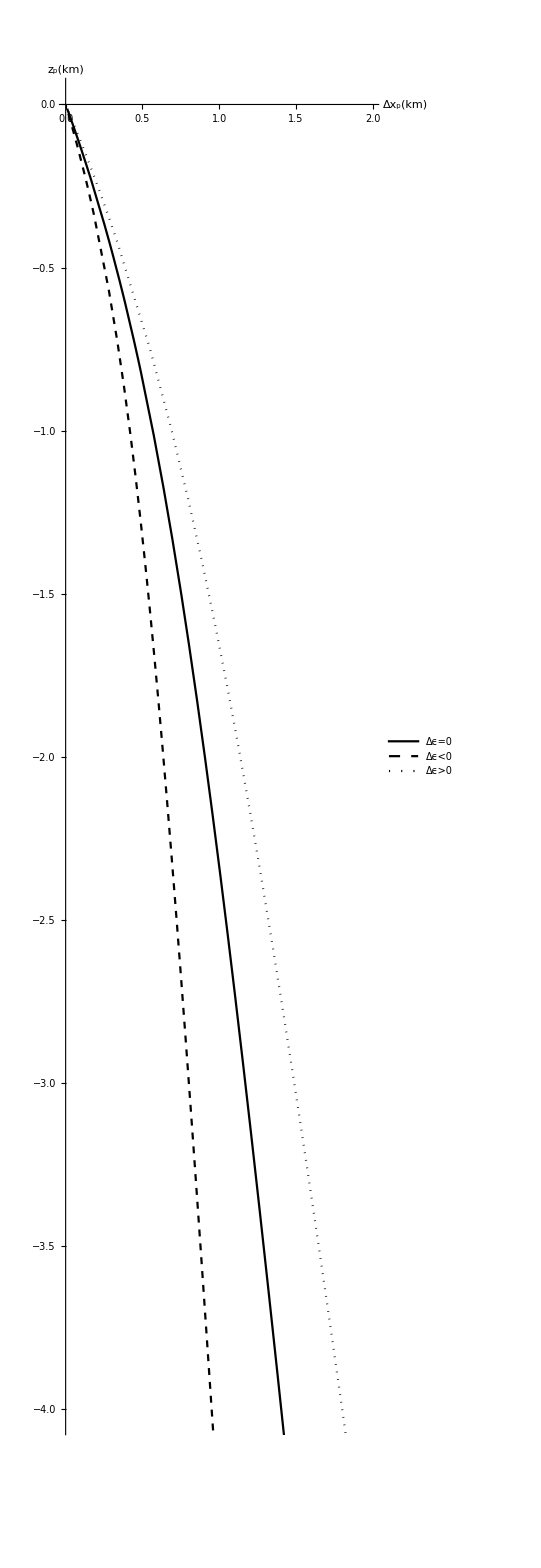

```mathematica
ParametricPlot[{{deex,-zpee},{deex1,-zpee1},{deex2,-zpee2}},{p,0.1,0.5},PlotRange->{{0,2},{-4,0}},AxesStyle->Black,AspectRatio->4,AxesLabel->{Style["Δx_p(km)",Black,FontSize->15],Style["z_p(km)",Black,FontSize->15]},PlotLegends->Placed[{"Δϵ=0","Δϵ<0","Δϵ>0"},Left],PlotStyle->{Directive[Black,Thick],Directive[Black,Dashed,Thick],Directive[Black,Dotted,Thick]}]
```

#### sensitivity with eta

```mathematica
parame3={v0->2,G->0.5,epslion->0.3,eta->0.05}
```

{v0→2,G→0.5,epslion→0.3,eta→0.05}

```mathematica
parame4={v0->2,G->0.5,epslion->0.3,eta->0.25}
```

{v0→2,G→0.5,epslion→0.3,eta→0.25}

```mathematica
deex3=Dxp/.parame3;
```

```mathematica
zpee3=Zpp/.parame3;
```

```mathematica
deex4=Dxp/.parame4;
```

```mathematica
zpee4=Zpp/.parame4;
```

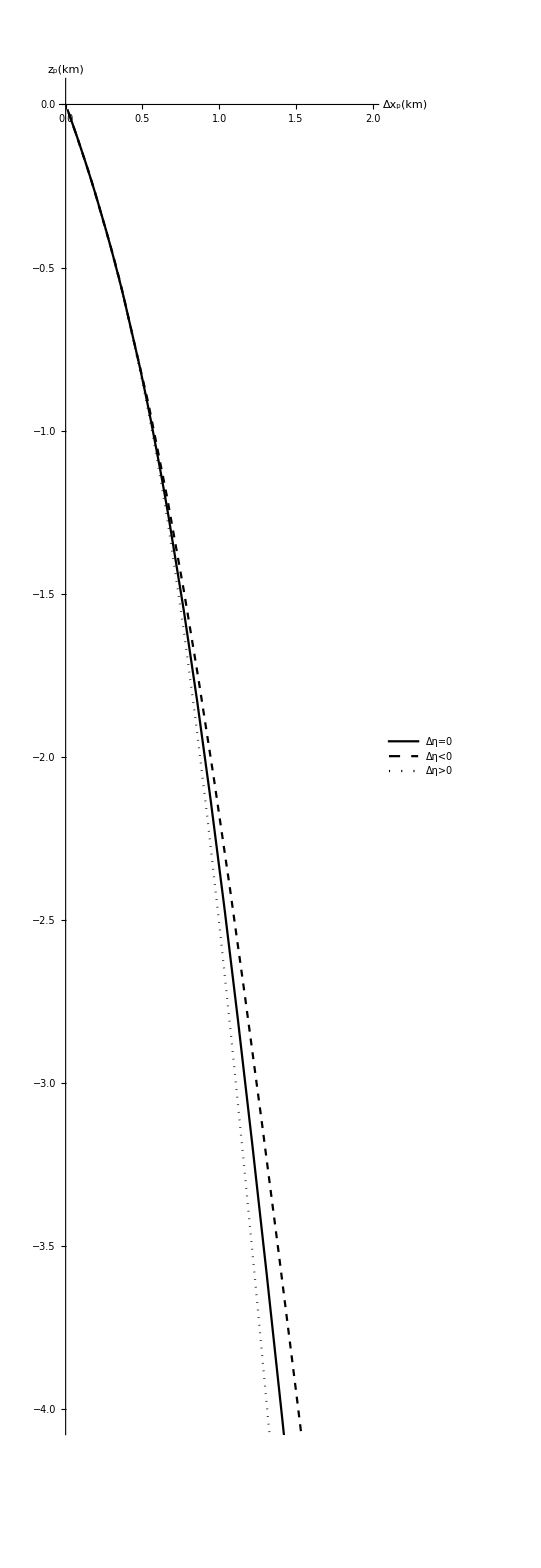

```mathematica
ParametricPlot[{{deex,-zpee},{deex3,-zpee3},{deex4,-zpee4}},{p,0.1,0.8},PlotRange->{{0,2},{-4,0}},AxesStyle->Black,AspectRatio->4,AxesLabel->{Style["Δx_p(km)",Black,FontSize->15],Style["z_p(km)",Black,FontSize->15]},PlotLegends->Placed[{"Δη=0","Δη<0","Δη>0"},Left],PlotStyle->{Directive[Black,Thick],Directive[Black,Dashed,Thick],Directive[Black,Dotted,Thick]}]
```